5)Используя таблицу значений функции f(x) в равноотстоящих точках
отрезка [0, 6], полученной в задании 1 при n = 10, выполнить следующие действия:
а) аппроксимировать с помощью метода наименьших квадратов функциюf(x) многочленом первой степени Q_1(x), проиллюстрировать
графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и Q_1(x) на одном чертеже);
б) аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом второйстепени Q_2(x), проиллюстрировать
графически;
в) найти многочлены наилучшего среднеквадратичного приближения
третьей и четвертой степеней(Q_3(x) и Q_4(x)) с помощью функции Fit
пакета Mathematica, проиллюстрировать графически;
г) вычислить значения функции f(x) и построенных многочленов Q_1(x), Q_2(x), Q_3(x) и Q_4(x) в точке x = 2,4316;
д) сравнить результаты, полученные впунктах а, б и в, изобразив на одном чертеже точки (x_i, f(x_i)) и графики функций Q_1(x), Q_2(x), Q_3(x) и Q_4(x).
Функция f(x):

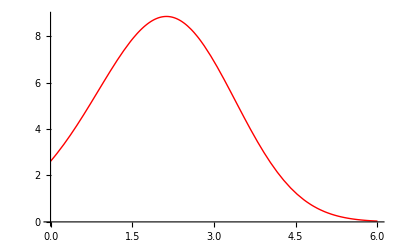

```mathematica
f[x_]= (x + √(π+1))* Exp[-4/39*√(x^5)+5*x/9+1/4];
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
graph = Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
tabl=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N;
TableForm[tabl]
```

0. | 2.61311
0.6 | 4.58895
1.2 | 6.88217
1.8 | 8.57075
2.4 | 8.65092
3. | 6.91907
3.6 | 4.29295
4.2 | 2.02528
4.8 | 0.712835
5.4 | 0.183836
6. | 0.0341457

a) Степень многочлена, которым будет аппроксимирована функция:

```mathematica
m = 1;
ACoeff1=Table[If[i+j!=0,∑_(k=0)^n (tabl[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.},{33.,138.6}}

Столбец свободных членов :

```mathematica
B1:=Table[If[i!=0,∑_(k=0)^n (tabl[[k+1,2]]*(tabl[[k+1,1]])^i), ∑_(l=0)^n tabl[[l+1,2]]], {i, 0, m}];B1
```

{45.474,96.5388}

Найдём значения a_i  с  помощью встроенной функции LinearSolve:

```mathematica
A1=LinearSolve[ACoeff1,B1]
```

{7.15546,-1.00715}

Тогда многочлен примет вид:

```mathematica
Q1[x_]=∑_(i=0)^m (A1[[i+1]]*x^i)
```

7.15546-1.00715 x

Изобразим полученный многочлен :

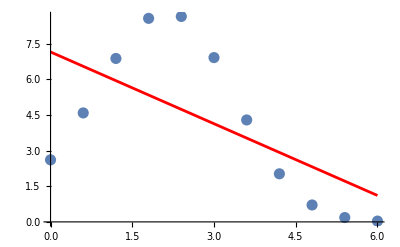

```mathematica
graphD=ListPlot[tabl,PlotStyle->{Darker,PointSize[0.02]}];
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Red];
Show[graphD,graphQ1]
```

Аналогичным образом найдём многочлен второй степени .

```mathematica
m=2;
ACoeff2=Table[If[i+j!=0,∑_(k=0)^n (tabl[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
B2:=Table[If[i!=0,∑_(k=0)^n (tabl[[k+1,2]]*(tabl[[k+1,1]])^i), ∑_(l=0)^n tabl[[l+1,2]]], {i, 0, m}];B2
```

{45.474,96.5388,265.809}

```mathematica
A2=LinearSolve[ACoeff2,B2]
```

{3.85981,2.65468,-0.610306}

```mathematica
Q2[x_]=∑_(i=0)^m (A2[[i+1]]*x^i)
```

3.85981+2.65468 x-0.610306 x^2

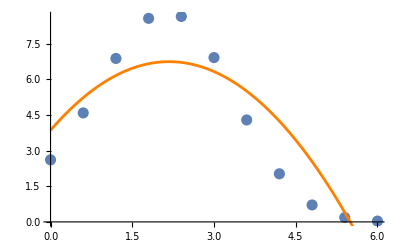

```mathematica
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Orange];
Show[graphD,graphQ2]
```

в)

```mathematica
Q3[x_]=Fit[tabl,{1,x^1,x^2,x^3},x]
Q4[x_]=Fit[tabl,{1,x^1,x^2,x^3,x^4},x]
```

1.78747+8.14255 x-3.00885 x^2+0.266505 x^3

2.29875+5.18379 x-0.543218 x^2-0.390997 x^3+0.0547918 x^4

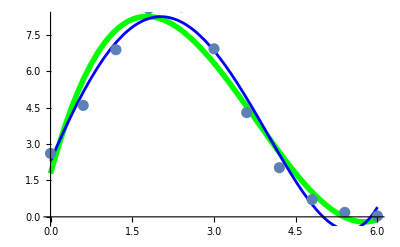

```mathematica
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->{Green,Thickness[0.01]}];
graphQ4=Plot[Q4[x],{x,a,b},PlotStyle->Blue];
Show[graphQ3,graphQ4,graphD]
```

г) Значения полученных многочленов в точке x0:

```mathematica
Print["Q1[x0]=",Q1[x0],", Q2[x0]=",Q2[x0],", Q3[x0]=",Q3[x0],", Q4[x0]=",Q4[x0]]
```

Q1[x0]=4.70647, Q2[x0]=6.70639, Q3[x0]=7.62814, Q4[x0]=7.98582

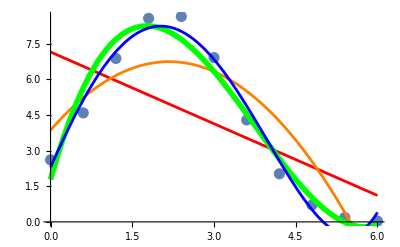

```mathematica
Show[graphD,graphQ1,graphQ2,graphQ3,graphQ4]
```

Как видно из графика, с увеличением степени многочлена аппроксимация методом наименьших квадратов даёт значения, всё более близкие к значениям исходной функции .